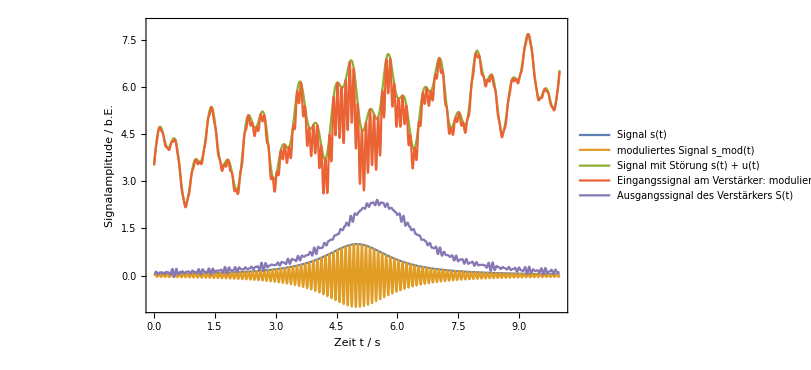

```mathematica
f=10;
refsig[t_]=Sin[f*2π t];
sig[t_]=1/(1+(t-5)^2);
stö[t_]=3.5+0.2t+0.01 t^2+Sin[0.9*2π t]+0.5Sin[2.3*2π t];
sigmst[t_]=sig[t]+stö[t];
modsig[t_]=refsig[t]*sig[t];
modsigmst[t_]=modsig[t]+stö[t];
produkt[t_]=modsigmst[t]*refsig[t]//Simplify;

p=Plot[
{sig[t],modsig[t],sigmst[t],modsigmst[t],5*NIntegrate[produkt[y],{y,t-10*1/f,t}]},
{t,0,10},
PlotRange->{-1,8},
PlotPoints->600,
ImageSize->600,
MaxRecursion->4,
PlotLegends->{"Signal s(t)","moduliertes Signal \n s_mod(t)","Signal mit Störung \n s(t) + u(t)","Eingangssignal\n am Verstärker:\n moduliertes \n Signal mit Störung \n s_mod(t) + u(t)","Ausgangssignal \n des Verstärkers S(t)"},
Frame->True,
FrameLabel->{"Zeit t / s","Signalamplitude / b.E."},
BaseStyle->17
]
```

```mathematica
Export[NotebookDirectory[]<>"../img/lockin.pdf",p]
```

/home/benjamin/Documents/Uni/FP1.git/1002-Halbleiter/stuff/../img/lockin.pdf